```mathematica
filelist=("E:\\_time_varying_data\\SmokeSim\\tif\\dsSmoke."<>IntegerString[#,10,3]<>".tif")&/@Range[0,499];
d=Import[filelist[[#]],"Image3D"]&/@Range[1,500];
offset=9;
tf=ColorData["RedGreenSplit"]
tffilelist=("E:\\_time_varying_data\\SmokeSim\\DSSmokeSideways100500\\dsSmoke."<>IntegerString[#,10,3]<>".tfi")&/@Range[0,499];
bincount=256;
```

ColorDataFunction[…]

{0,1/200,1/100,3/200,1/50,1/40,3/100,7/200,1/25,9/200,1/20,11/200,3/50,13/200,7/100,3/40,2/25,17/200,9/100,19/200,1/10,21/200,11/100,23/200,3/25,1/8,13/100,27/200,7/50,29/200,3/20,31/200,4/25,33/200,17/100,7/40,9/50,37/200,19/100,39/200,1/5,41/200,21/100,43/200,11/50,9/40,23/100,47/200,6/25,49/200,1/4,51/200,13/50,53/200,27/100,11/40,7/25,57/200,29/100,59/200,3/10,61/200,31/100,63/200,8/25,13/40,33/100,67/200,17/50,69/200,7/20,71/200,9/25,73/200,37/100,3/8,19/50,77/200,39/100,79/200,2/5,81/200,41/100,83/200,21/50,17/40,43/100,87/200,11/25,89/200,9/20,91/200,23/50,93/200,47/100,19/40,12/25,97/200,49/100,99/200,1/2,101/200,51/100,103/200,13/25,21/40,53/100,107/200,27/50,109/200,11/20,111/200,14/25,113/200,57/100,23/40,29/50,117/200,59/100,119/200,3/5,121/200,61/100,123/200,31/50,5/8,63/100,127/200,16/25,129/200,13/20,131/200,33/50,133/200,67/100,27/40,17/25,137/200,69/100,139/200,7/10,141/200,71/100,143/200,18/25,29/40,73/100,147/200,37/50,149/200,3/4,151/200,19/25,153/200,77/100,31/40,39/50,157/200,79/100,159/200,4/5,161/200,81/100,163/200,41/50,33/40,83/100,167/200,21/25,169/200,17/20,171/200,43/50,173/200,87/100,7/8,22/25,177/200,89/100,179/200,9/10,181/200,91/100,183/200,23/25,37/40,93/100,187/200,47/50,189/200,19/20,191/200,24/25,193/200,97/100,39/40,49/50,197/200,99/100,199/200,1,201/200}

{0,1/200,1/100,3/200,1/50,1/40,3/100,7/200,1/25,9/200,1/20,11/200,3/50,13/200,7/100,3/40,2/25,17/200,9/100,19/200,1/10,21/200,11/100,23/200,3/25,1/8,13/100,27/200,7/50,29/200,3/20,31/200,4/25,33/200,17/100,7/40,9/50,37/200,19/100,39/200,1/5,41/200,21/100,43/200,11/50,9/40,23/100,47/200,6/25,49/200,1/4,51/200,13/50,53/200,27/100,11/40,7/25,57/200,29/100,59/200,3/10,61/200,31/100,63/200,8/25,13/40,33/100,67/200,17/50,69/200,7/20,71/200,9/25,73/200,37/100,3/8,19/50,77/200,39/100,79/200,2/5,81/200,41/100,83/200,21/50,17/40,43/100,87/200,11/25,89/200,9/20,91/200,23/50,93/200,47/100,19/40,12/25,97/200,49/100,99/200,1/2,101/200,51/100,103/200,13/25,21/40,53/100,107/200,27/50,109/200,11/20,111/200,14/25,113/200,57/100,23/40,29/50,117/200,59/100,119/200,3/5,121/200,61/100,123/200,31/50,5/8,63/100,127/200,16/25,129/200,13/20,131/200,33/50,133/200,67/100,27/40,17/25,137/200,69/100,139/200,7/10,141/200,71/100,143/200,18/25,29/40,73/100,147/200,37/50,149/200,3/4,151/200,19/25,153/200,77/100,31/40,39/50,157/200,79/100,159/200,4/5,161/200,81/100,163/200,41/50,33/40,83/100,167/200,21/25,169/200,17/20,171/200,43/50,173/200,87/100,7/8,22/25,177/200,89/100,179/200,9/10,181/200,91/100,183/200,23/25,37/40,93/100,187/200,47/50,189/200,19/20,191/200,24/25,193/200,97/100,39/40,49/50,197/200,99/100,199/200,1}

{859068,11793,9686,17649,7434,6795,6292,9559,3610,3024,4915,1983,1887,1655,2883,1287,1183,1110,2080,839,838,1614,723,725,674,1278,582,631,583,1152,585,540,1078,466,463,478,810,429,432,401,737,376,352,705,343,298,297,547,287,257,572,248,258,260,540,242,256,228,539,262,254,432,221,257,213,440,196,225,226,384,186,185,422,195,179,164,352,164,169,179,340,177,159,333,186,155,159,330,155,151,314,145,158,155,319,145,141,146,297,142,153,296,143,161,143,294,139,131,156,264,139,147,269,111,128,114,255,114,139,117,225,108,116,240,110,127,120,238,137,124,235,128,136,109,241,116,105,119,240,110,126,253,133,109,117,257,125,117,95,211,122,107,205,94,104,87,213,111,105,113,186,101,135,209,129,113,110,203,77,120,182,100,87,78,164,94,94,81,192,84,86,181,75,85,48,133,88,72,74,160,71,70,147,71,63,50,86,33,44,42,513}

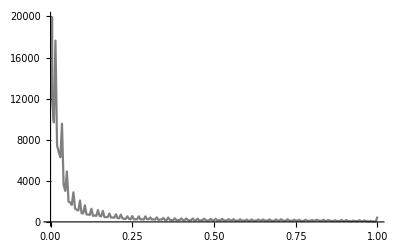

201

```mathematica
i=160;
a=Flatten[ImageData[d[[i]]]];
h=HistogramList[a,bincount];
h[[1]]
x=Take[h[[1]],Length[h[[1]]]-1]
y=h[[2]]
p=ListLinePlot[Transpose[{x,y}],PlotRange->{{0,1},{0,20000}},ColorFunction->(GrayLevel[#]&),PlotLegends->"intensity histogram"]
Export[NotebookDirectory[]<>ToString[160]<>".png",p,ImageSize->640];
Length[y]
```

200

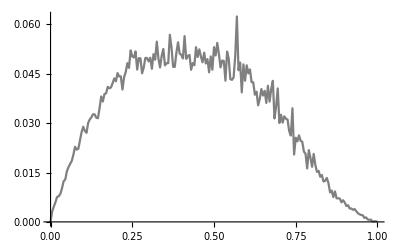

```mathematica
list=d[[i-offset;;i]];
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,list];
b=Flatten[ImageData[std]];
numofbins=Length[y]-1
bins=ConstantArray[0,Length[y]];
sumstd=ConstantArray[0,Length[y]];
Table[j=IntegerPart[a[[i]]*numofbins]+1;bins[[j]]++;sumstd[[j]]+=b[[i]],{i,1,Length[a]}];
stds=sumstd/bins;
p2=ListLinePlot[Transpose[{x,stds}],ColorFunction->(GrayLevel[#]&),PlotLegends->"volatility histogram"]
Export[NotebookDirectory[]<>ToString[i]<>"_std.png",p2,ImageSize->640];
```

160

{{0,-Graphics-},{0.0588235,-Graphics-},{0.117647,-Graphics-},{0.176471,-Graphics-},{0.235294,-Graphics-},{0.294118,-Graphics-},{0.352941,-Graphics-},{0.411765,-Graphics-},{0.470588,-Graphics-},{0.529412,-Graphics-},{0.588235,-Graphics-},{0.647059,-Graphics-},{0.705882,-Graphics-},{0.764706,-Graphics-},{0.823529,-Graphics-},{0.882353,-Graphics-},{0.941176,-Graphics-},{1,-Graphics-}}

Blend[Transpose[{intensity,colors}],#1]&

Blend[Transpose[{intensity,colors2}],#1]&

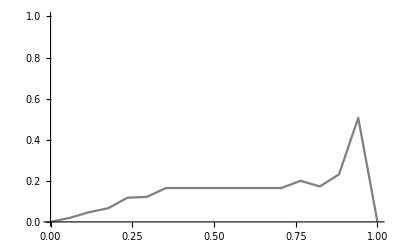

-Graphics3D-

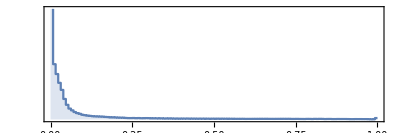

```mathematica
i=160;
tf=Import[tffilelist[[i]],"XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgba=(#/255.&)/@Transpose[{r,g,b,a}];
colors=RGBColor/@rgba;
defaultcolorfunction=(Blend[{{0., RGBColor[0.05635, 0.081, 0.07687, 0.0166234]}, {0.1, RGBColor[0.8877, 0.2636, 0., 0.114961]}, {0.66, RGBColor[1., 0.9658, 0.4926, 0.665652]}, {1., RGBColor[1., 0.6436, 0.03622, 1.]}}, #1] & );
Transpose[{intensity,colors}]
colorfunction=(Blend[Transpose[{intensity,colors}], #1] & )
rgb=(#/255.&)/@Transpose[{r,g,b}];
colors2=RGBColor/@rgb;
colorfunction2=(Blend[Transpose[{intensity,colors2}], #1] & )
opacity=(#/255.&)/@a;
ListLinePlot[Transpose[{intensity,opacity}],PlotRange->{{0,1},{0,1}},ColorFunction->colorfunction2,PlotLegends->"transfer function"]
Image3D[d[[i]],ColorFunction->colorfunction]
ImageHistogram[d[[i]]]
```

```mathematica
(*start=1+offset;end=500;step=20;
Do[
end2=Min[j+step-1,end];
Module[{list,std,a,b,h,x,y,bins,sumstd,stds,plot1,plot2,result},
result=ParallelTable[
list=d[[i-offset;;i]];
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,list];
a=Flatten[ImageData[d[[i]]]];
b=Flatten[ImageData[std]];
h=HistogramList[a];
x=Take[h[[1]],Length[h[[1]]]-1];
y=h[[2]];
plot1=ListLinePlot[Transpose[{x,y}],PlotRange->{{0,1},{0,20000}},ColorFunction->(GrayLevel[#]&),PlotLegends->"intensity histogram"];

bins=ConstantArray[0,Length[y]];
sumstd=ConstantArray[0,Length[y]];
Table[n=IntegerPart[a[[m]]*20]+1;bins[[n]]++;sumstd[[n]]+=b[[m]],{m,1,Length[a]}];
stds=sumstd/bins;
plot2=ListLinePlot[Transpose[{x,stds}],ColorFunction->(GrayLevel[#]&),PlotLegends->"volatility histogram"];
{plot1,plot2}
,{i,j,end2}];
num=Range[j,end2];
MapIndexed[
Export[NotebookDirectory[]<>"smoke2\\"<>IntegerString[num[[First[#2]]],10,3]<>".png",First[#],ImageSize->{640,280}]&;Export[NotebookDirectory[]<>"smoke2_std\\"<>IntegerString[num[[First[#2]]],10,3]<>".png",Last[#],ImageSize->{640,280}]&
,result];
]
,{j,start,end,step}]*)
```

```mathematica
x
y
x2=h[[1]]
sum=Total[y]
alpha:=Interpolation[Transpose[{intensity,opacity}]]
hist[i_]:=First@FirstPosition[x2,_?(i<#&)]-1
probability[i_]:=N[y[[hist[i]]]/sum]
entropy[i_]:=Module[{p},p=probability[i];-p*Log[p]]
signiﬁcance[i_]:=alpha[i]*entropy[i]
energy[x1_,x2_]:=Sum[signiﬁcance[i],{i,x1,x2,1/255.0}]
```

{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1}

{934910,19822,8800,5682,4199,3405,2848,2195,2145,1962,1880,1533,1545,1539,1543,1261,1383,1156,1002,677,513}

{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1,21/20}

1000000

```mathematica
intensity
opacity
```

{0,0.0588235,0.117647,0.176471,0.235294,0.294118,0.352941,0.411765,0.470588,0.529412,0.588235,0.647059,0.705882,0.764706,0.823529,0.882353,0.941176,1}

{0.,0.0196078,0.0470588,0.0666667,0.117647,0.121569,0.164706,0.164706,0.164706,0.164706,0.164706,0.164706,0.164706,0.2,0.172549,0.231373,0.505882,0.}

```mathematica
interval=Table[{intensity[[i]],intensity[[i+1]]},{i,Length[intensity]-1}]
```

{{0,0.0588235},{0.0588235,0.117647},{0.117647,0.176471},{0.176471,0.235294},{0.235294,0.294118},{0.294118,0.352941},{0.352941,0.411765},{0.411765,0.470588},{0.470588,0.529412},{0.529412,0.588235},{0.588235,0.647059},{0.647059,0.705882},{0.705882,0.764706},{0.764706,0.823529},{0.823529,0.882353},{0.882353,0.941176},{0.941176,1}}

```mathematica
edges=energy[#1,#2]&@@@interval
mean=Mean[edges];
Length[edges];
Length[opacity];
MapIndexed[#1&,edges];
max=0;
min = 255;
imin=-1;
imax=-1;
Do[max=If[edges[[i]]>max && opacity[[i]]>0,imax=i;edges[[i]],max];min=If[edges[[i]]<min&& opacity[[i]]>0,imin=i;edges[[i]],min],{i,1,Length[edges]}];
```

{0.00943657,0.0336089,0.0319838,0.0369971,0.0388463,0.0383863,0.0356009,0.0337954,0.0316637,0.0280239,0.0263214,0.0260611,0.0280748,0.0258144,0.0253635,0.0444901,0.0308605}

```mathematica
First@FirstPosition[edges,_?(#==Max[edges]&)]
First@FirstPosition[edges,_?(#==Min[edges]&)]
Position[edges,_?(#>0.02&)]
```

16

1

{{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17}}

```mathematica
Table[If[edges[[i]]>mean,edges[[i]]-1/255.0,edges[[i]]+1/255.0],{i,1,Length[edges]}]
```

{0.0133581,0.0296873,0.0280622,0.0330756,0.0349247,0.0344648,0.0316793,0.0298738,0.0277421,0.0319455,0.030243,0.0299826,0.0319964,0.029736,0.0292851,0.0405685,0.0347821}

```mathematica
opacity2=opacity
alpha=Interpolation[Transpose[{intensity,opacity2}]]
Length[opacity2]
Do[Module[{d,m,list},
d=1/255.0;
alpha=Interpolation[Transpose[{intensity,opacity2}]];
edges=energy[#1,#2]&@@@interval;
m=Mean[edges];
list=Table[If[edges[[i]]>m,-d,d],{i,1,Length[edges]}]
],{100}]
```

{0.,0.0196078,0.0470588,0.0666667,0.117647,0.121569,0.164706,0.164706,0.164706,0.164706,0.164706,0.164706,0.164706,0.2,0.172549,0.231373,0.505882,0.}

InterpolatingFunction[{{0., 1.}}, <>]

18

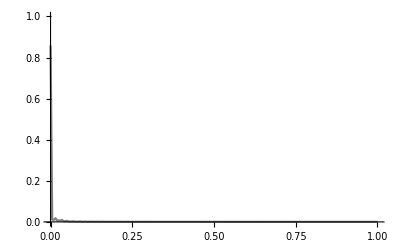

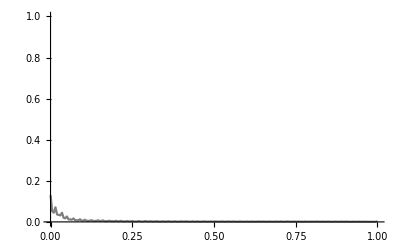

```mathematica
intensityfunction=Take[h[[1]],Length[h[[1]]]-1];
ListLinePlot[Transpose[{intensityfunction,probability[#]&/@intensityfunction}],PlotRange->{{0,1},{0,1}},ColorFunction->colorfunction2,PlotLegends->"probability"]
ListLinePlot[Transpose[{intensityfunction,entropy[#]&/@intensityfunction}],PlotRange->{{0,1},{0,1}},ColorFunction->colorfunction2,PlotLegends->"entropy"]
```

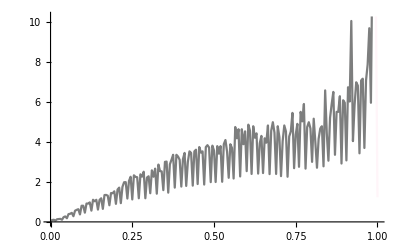

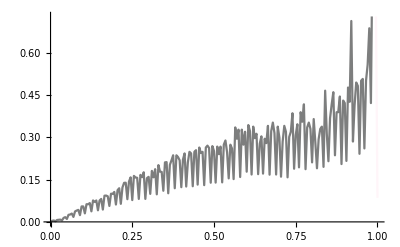

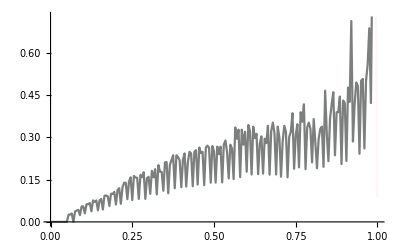

160

{{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1,21/20},{934910,19822,8800,5682,4199,3405,2848,2195,2145,1962,1880,1533,1545,1539,1543,1261,1383,1156,1002,677,513}}

D:\document\work\time-varying-visualization\smoke160.tfi

```mathematica
entropymean=Mean[entropy[#]&/@intensityfunction];
op=entropymean/entropy[#]&/@intensityfunction//Rescale//If[#<0.02,0,#]&/@#&;
op2=entropymean/entropy[#]&/@intensityfunction//Rescale;
op3=entropymean/entropy[#]&/@intensityfunction;
ListLinePlot[Transpose[{intensityfunction,op3}],ColorFunction->colorfunction2,PlotLegends->"opacity"]
ListLinePlot[Transpose[{intensityfunction,op2}],ColorFunction->colorfunction2,PlotLegends->"normalized opacity"]
ListLinePlot[Transpose[{intensityfunction,op}],ColorFunction->colorfunction2,PlotLegends->"clipped normalized opacity"]
```

```mathematica
({#1,#2,#3}&)@@@{{11,12,13},{21,22,23},{31,32,33},{41,42,43}}
({#[[1]],#[[2]],#[[3]]}&)/@{{11,12,13},{21,22,23},{31,32,33},{41,42,43}}
```

{{11,12,13},{21,22,23},{31,32,33},{41,42,43}}

{{11,12,13},{21,22,23},{31,32,33},{41,42,43}}

```mathematica
(* unwanted opacity 0.0409807, 0.0400936, 0.0326559 in 15.png, 16.png, 22.png *)
i=16;
tf=Import[tffilelist[[i]],"XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgb=(#/255.&)/@Transpose[{r,g,b}];
opacity=(#/255.&)/@a;
colors2=RGBColor/@rgb;
colorfunction2=(Blend[Transpose[{intensity,colors2}], #1] & );

a=Flatten[ImageData[d[[i]]]];
h=HistogramList[a,bincount];
intensityfunction=Take[h[[1]],Length[h[[1]]]-1];
sum:=Total[h[[2]]];
hist[i_]:=First@FirstPosition[h[[1]],_?(i<#&)]-1;
probability[i_]:=N[h[[2]][[hist[i]]]/sum];
entropy[i_]:=Module[{p},p=probability[i];-p*Log[p]];
entropymean=Mean[entropy[#]&/@intensityfunction];
op=entropymean/entropy[#]&/@intensityfunction//Rescale//If[#<0.02,0,#]&/@#&;
Sort[op]
```

{0,0,0,0,0,0.0279125,0.0279125,0.0286598,0.0329896,0.0359,0.0454805,0.0525606,0.0537447,0.061287,0.0681838,0.0691529,0.0722281,0.0733133,0.0744308,0.0767688,0.0792554,0.0792554,0.080559,0.0819055,0.0819055,0.0847359,0.0847359,0.0862247,0.0877662,0.0910186,0.0910186,0.0927361,0.0945192,0.0945192,0.0963717,0.104566,0.106837,0.106837,0.109208,0.109208,0.111687,0.111687,0.114282,0.114282,0.114282,0.117,0.117,0.125997,0.125997,0.129314,0.132812,0.132812,0.132812,0.132812,0.132812,0.136506,0.136506,0.136506,0.136506,0.140414,0.140414,0.144556,0.148953,0.148953,0.148953,0.148953,0.15363,0.15363,0.15363,0.15363,0.15363,0.15363,0.158616,0.158616,0.158616,0.163942,0.163942,0.163942,0.163942,0.163942,0.169645,0.169645,0.169645,0.175767,0.175767,0.175767,0.175767,0.175767,0.175767,0.175767,0.182358,0.182358,0.182358,0.182358,0.189473,0.189473,0.189473,0.189473,0.19718,0.19718,0.205558,0.205558,0.205558,0.205558,0.214698,0.214698,0.214698,0.214698,0.214698,0.214698,0.214698,0.214698,0.214698,0.214698,0.214698,0.214698,0.224712,0.224712,0.224712,0.224712,0.224712,0.224712,0.224712,0.224712,0.224712,0.235735,0.235735,0.235735,0.235735,0.235735,0.235735,0.247929,0.247929,0.247929,0.247929,0.247929,0.247929,0.247929,0.247929,0.247929,0.261496,0.261496,0.261496,0.261496,0.276684,0.276684,0.276684,0.276684,0.276684,0.293811,0.293811,0.293811,0.293811,0.293811,0.293811,0.313278,0.313278,0.313278,0.313278,0.313278,0.313278,0.313278,0.313278,0.313278,0.33561,0.33561,0.33561,0.33561,0.33561,0.33561,0.33561,0.33561,0.33561,0.361504,0.361504,0.361504,0.361504,0.361504,0.391903,0.391903,0.391903,0.391903,0.428119,0.428119,0.428119,0.472035,0.472035,0.472035,0.526454,0.595743,0.595743,0.595743,0.595743,0.595743,0.687115,0.813413,0.813413,1.,1.,1.,1.}

```mathematica
opacityfunction=Interpolation[Transpose[{intensityfunction,op}]];
rgba=Append[List@@colorfunction2[#],opacityfunction[#]]&/@intensityfunction;
denormalized=(IntegerPart[255#]&)/@rgba;
r=Transpose[{intensityfunction,denormalized}]//Flatten[#]&/@#&;
strlist={ToString[#[[1]]],ToString[#[[2]]],ToString[#[[3]]],ToString[#[[4]]],ToString[#[[5]]]}&/@r;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({intensity=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xml=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}];
Export[NotebookDirectory[]<>"smoke"<>IntegerString[i,10,3]<>".tfi",xml,"XML"]
```

D:\document\work\time-varying-visualization\smoke016.tfi

```mathematica
CloseKernels[];
LaunchKernels[8];
i=160;
tf=Import[tffilelist[[i]],"XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgb=(#/255.&)/@Transpose[{r,g,b}];
opacity=(#/255.&)/@a;
colors2=RGBColor/@rgb;
colorfunction2=(Blend[Transpose[{intensity,colors2}], #1] & );
a=Flatten[ImageData[d[[i]]]];
h=HistogramList[a,bincount];
intensityfunction=Take[h[[1]],Length[h[[1]]]-1];
Length[h[[2]]]
```

201

```mathematica
(* unwanted opacity 0.0409807, 0.0400936, 0.0326559 in 15.png, 16.png, 22.png *)
```

```mathematica
start=1+offset;end=500;step=40;
start=1;
Do[
end2=Min[j+step-1,end];
Module[{a,result,h,intensityfunction,sum,hist,probability,entropy,entropymean,op,opacityfunction,rgba,denormalized,r,strlist,alphaMode,gammaValue,domain,threshold,k,intensity,split,colorL,keylist,keys,TransFuncIntensity,VoreenData},
result=ParallelTable[
a=Flatten[ImageData[d[[i]]]];
h=HistogramList[a,bincount];
intensityfunction=Take[h[[1]],Length[h[[1]]]-1];
sum:=Total[h[[2]]];
hist[i_]:=First@FirstPosition[h[[1]],_?(i<#&)]-1;
probability[i_]:=N[h[[2]][[hist[i]]]/sum];
entropy[i_]:=Module[{p},p=probability[i];-p*Log[p]];

entropymean=Mean[entropy[#]&/@intensityfunction];
(*op=entropymean/entropy[#]&/@intensityfunction//Rescale//If[#<0.02,0,#]&/@#&;*)
op=entropymean/entropy[#]&/@intensityfunction//Rescale;
opacityfunction=Interpolation[Transpose[{intensityfunction,op}]];
rgba=Append[List@@colorfunction2[#],opacityfunction[#]]&/@intensityfunction;
denormalized=(IntegerPart[255#]&)/@rgba;
r=Transpose[{intensityfunction,denormalized}]//Flatten[#]&/@#&;
strlist={ToString[#[[1]]],ToString[#[[2]]],ToString[#[[3]]],ToString[#[[4]]],ToString[#[[5]]]}&/@r;

alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({intensity=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}]
,{i,j,end2}];
num=Range[j,end2];
MapIndexed[
Export[NotebookDirectory[]<>"tfi\\"<>IntegerString[num[[First[#2]]]-1,10,3]<>".tfi",#, "XML"]&,result]
]
,{j,start,end,step}]
```

```mathematica
Do[Module[{tf,intensity,r,g,b,a,rgba,colors,colorfunction,img},
tf=Import[NotebookDirectory[]<>"tfi\\"<>IntegerString[i-1,10,3]<>".tfi","XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgba=(#/255.&)/@Transpose[{r,g,b,a}];
colors=RGBColor/@rgba;
colorfunction=(Blend[Transpose[{intensity,colors}], #1] & );
img=Image3D[d[[i]],ColorFunction->colorfunction];
Export[NotebookDirectory[]<>"png\\"<>IntegerString[i-1,10,3]<>".png",img,ImageSize->640]
]
,{i,1,500}]
```